```mathematica
Cv[T_,θE_]:=3 NA kB(θE/T)^2 Exp[θE/T]/(Exp[θE/T]-1)^2
```

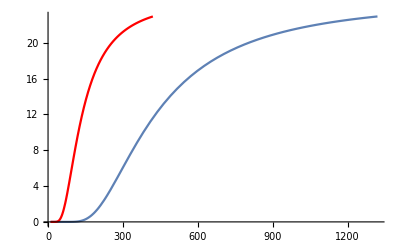

```mathematica
NA=6.022 10^23;
kB=1.38*10^-23;

p1=Plot[Cv[T,1320],{T,10,1320}];  (*Diamond*)
p2=Plot[Cv[T,420],{T,10,420},PlotStyle->Red];  (*Hg*)
Show[p1,p2]
```